# Kitaev model with B field

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
(*MaTeX`Developer`ResetConfiguration[]*)
```

```mathematica
t0 = AbsoluteTime[];
```

3.822369319362821×10^9

### Hamiltonian

```mathematica
ClearAll[J,k,κ,h,n]
```

```mathematica
r[J_]=J;
s[k_,J_]=-2J Cos[k/2];
α[k_,κ_] = 2 κ Sin [k];
β[k_,κ_] =  2 κ Sin [k/2];
γ[h_] = -h;
```

```mathematica
H[k_,n_, J_,κ_,h_] := SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-α[k,κ], α[k,κ]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[ ((i==1)∨(i==2n+4)), ⅈ γ[h] , - ⅈ γ[h] ], 
															If[EvenQ[Min[i,j]], -(i-j) ⅈ s[k,J] , -(i-j) ⅈ r[J]] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],β[k,κ], -β[k,κ]] ]
},					
	{2n+ 4,2n+ 4}					]
```

```mathematica
Energies[n_,J_,κ_ ,h_, P_] :=  Table[  N@ {   k, Chop@Sort[Eigenvalues[ N@ H[k, n, J,κ,h] ]]    }     , {k,0,2π , 2π/(P-1)}]
```

```mathematica
n = 200;
P = 500;
J = 1;
```

```mathematica
dispersion[E_,P_,n_]:= Transpose[    Table[  { E⟦i⟧⟦1⟧ , E⟦i⟧⟦2⟧⟦j⟧} , {i,1,P} , {j,1,2*n+4}]  ]
```

```mathematica
edge[D_,n_] := D⟦ {n+1,n+2,n+3,n+4} ⟧
bulk[D_,n_] := D⟦ {1,n,n+5,2n+4} ⟧
```

### Dispersion

#### in plane field in a direction

```mathematica
{hx,hy,hz}=0.85 {1,1,-2}/Sqrt[6]
```

{0.347011,0.347011,-0.694022}

```mathematica
hx hy hz//N
```

-0.0835718

```mathematica
Sqrt[hx^2+hy^2+hz^2]//N
```

0.85

```mathematica
Timing[Ea = Energies[n,1,hx hy hz,hz, P]]⟦1⟧ //Quiet
```

33.0313

```mathematica
Da = dispersion[Ea,P,n];
```

```mathematica
edge[D_,n_] := D⟦ {n+1,n+2,n+3,n+4} ⟧
bulk[D_,n_] := D⟦ {1,n,n+5,2n+4} ⟧
```

```mathematica
edA = edge[ Da,n];
bulkA = bulk[ Da,n];
```

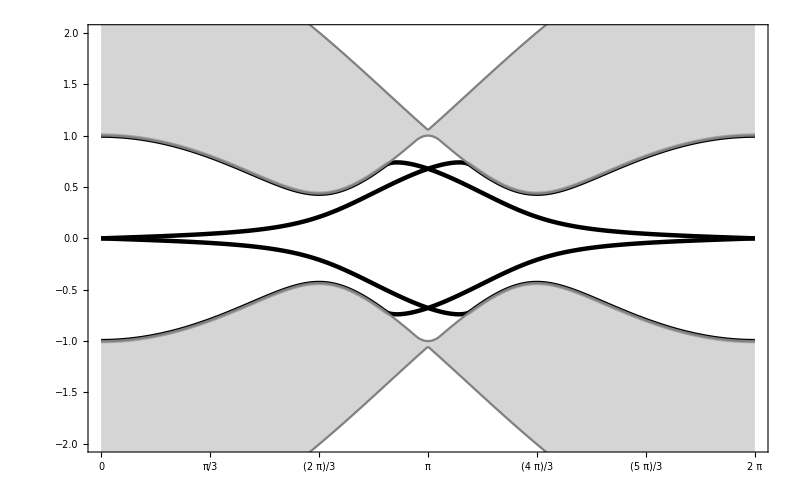

```mathematica
Show[ListPlot[ edA , Joined->True ,  PlotRange-> {-2,2}  , FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{a} ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π , 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} ,   FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800],

ListPlot[ bulkA ,  Joined->True , FrameLabel->{k , ϵ }   ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray , FrameTicks->{{ -π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800 ] ]
```

```mathematica
(*ListPlot[ Da , Joined->True ,  PlotRange-> All , FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{a} ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800] *)
```

#### in plane field in b direction

```mathematica
{hx,hy,hz}= 0.85 {-1,1,0}/Sqrt[2]
```

{-0.601041,0.601041,0.}

```mathematica
hx hy hz//N
```

0.

```mathematica
Sqrt[hx^2+hy^2+hz^2]//N
```

0.85

```mathematica
Timing[Eb = Energies[n,1,hx hy hz,hz, P]]⟦1⟧ //Quiet
```

27.6094

```mathematica
Db= dispersion[Eb,P,n];
```

```mathematica
edB = edge[ Db,n];
bulkB = bulk[ Db,n];
```

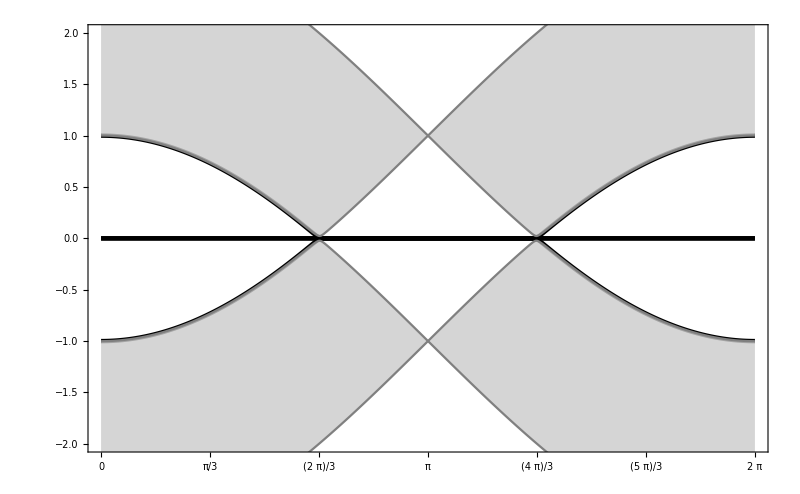

```mathematica
Show[ListPlot[ edB, Joined->True ,  PlotRange-> {-2,2} ,  FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{b} ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800],

ListPlot[ bulkB ,  Joined->True , FrameLabel->{k , ϵ }   ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray , FrameTicks->{{ -π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800 ] ]
```

#### out of plane field in c direction

```mathematica
{hx,hy,hz}= 0.85{1,1,1}/Sqrt[3]//N
```

{0.490748,0.490748,0.490748}

```mathematica
hx hy hz//N
```

0.118188

```mathematica
Sqrt[hx^2+hy^2+hz^2]//N
```

0.85

```mathematica
Timing[Ec = Energies[n,1,hx hy hz,hz, P]]⟦1⟧ //Quiet
```

31.1094

```mathematica
Dc= dispersion[Ec,P,n];
```

```mathematica
edC = edge[ Dc,n];
bulkC = bulk[ Dc,n];
```

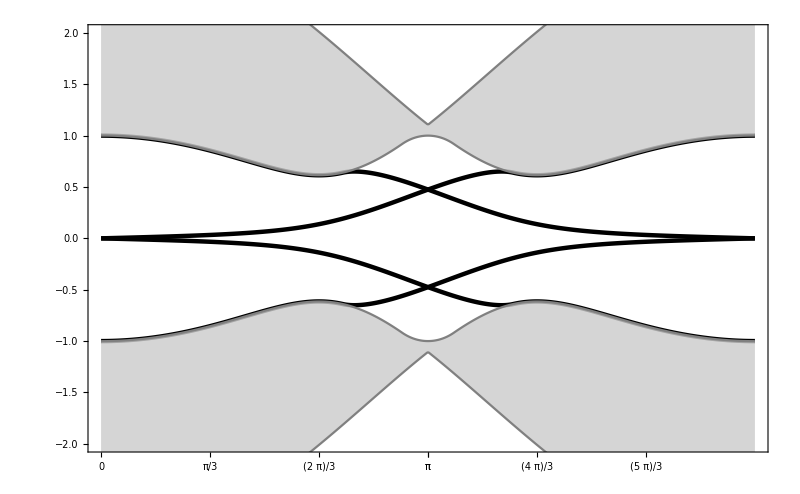

```mathematica
Show[ListPlot[ edC, Joined->True ,  PlotRange-> {-2,2} ,   FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{c} ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800],

ListPlot[ bulkC ,  Joined->True , FrameLabel->{q , ϵ }   ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray , FrameTicks->{{ -π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800 ] ]
```

#### out of plane in x = (0,1,-1) direction

```mathematica
{hx,hy,hz}= 0.85 {0,1,-1}/Sqrt[2]
```

{0.,0.601041,-0.601041}

```mathematica
hx hy hz//N
```

0.

```mathematica
Sqrt[hx^2+hy^2+hz^2]//N
```

0.85

```mathematica
Timing[Ex = Energies[n,1,hx hy hz,hz, P]]⟦1⟧ //Quiet
```

27.6406

```mathematica
Dx= dispersion[Ex,P,n];
```

```mathematica
edx = edge[ Dx,n];
bulkx = bulk[ Dx,n];
```

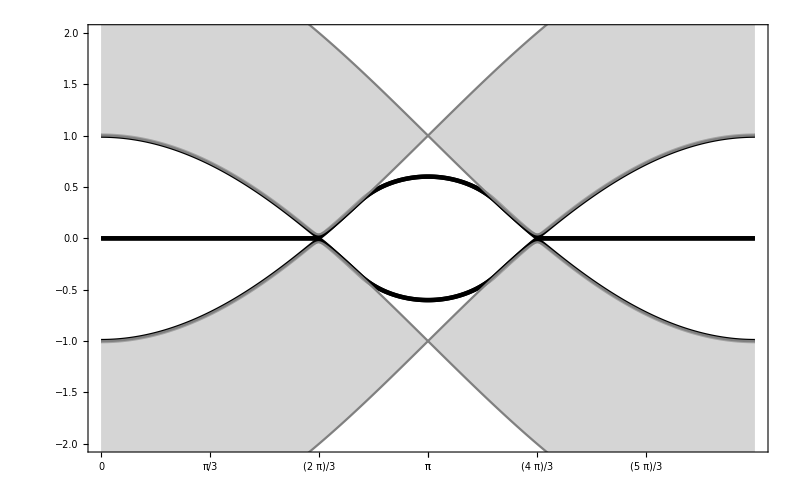

```mathematica
Show[ListPlot[ edx, Joined->True ,  PlotRange-> {-2,2} ,  FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, [ \\text{link-}x ] ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800],

ListPlot[ bulkx ,  Joined->True , FrameLabel->{k , ϵ }   ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray , FrameTicks->{{ -π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800 ] ]
```

### time elapsed

```mathematica
tf= AbsoluteTime[];
(tf-t0)/60
```

4.60787725